```mathematica
Clear[LaneEmdenSolve]

R=6.96*10^8;
LaneEmdenSolve[n_,ξmax_:R,rhoC_:1.53*10^5,K_:5.556*10^9,G_:6.67*10^-11,C_:3*10^8]:=
Module[
{eps=10^-7,
sol,
a,
theta,deltheta,
r,rmax,
rho,delrho,
P,delP,
m,
g,
rat,arat,
B,
T,delT,
σ,Φ,L,
kb,mh,mu
},

sol=
NDSolve[{
θ''[ξ]+(2/ξ) θ'[ξ]+θ[ξ]^n==0,
θ[eps]==1-eps^2/6,
θ'[eps]==-eps/3
},θ,{ξ,eps,ξmax}](*,MaxStepSize->0.05][[1]]*);

a=If[
n==0,√(K/(4Pi G rhoC))(*constant-density sphere*),
√((K (n+1)rhoC^(1/n-1))/(4Pi G))
];
(*theta=θ/. sol;*)
theta=θ/. sol[[1]];
(*theta[ξ_]:=Evaluate[θ[ξ]/. sol];*)
deltheta[ξ_]:=theta'[ξ];

r[ξ_]:=a ξ;
rmax = a ξmax;

(* define xi = r/a *)
rho[r_]:= rhoC theta[r/a]^n;
delrho[r_]:=(rhoC n/a) theta[r/a]^(n-1)deltheta[r/a];

(*Solve mass equation*)
m=
NDSolveValue[{
M'[r]==4 Pi a^2 (r/a)^2 rho[r],
M[0]==4 Pi rhoC (a*eps)^3/3
},M,{r,0,rmax}];

(*Hydrostatic equilibrium*)
P[r_]:=If[
n==0,K*rho[r],
K*rho[r]^(1+1/n)
];
delP[r_]:=P'[r];

(*g(r)*)
g[r_]:=(G m[r])/r^2;

(* ratio functions *)
rat[r_]:=delP[r]/(rho[r]g[r]);
B[r_]:=delP[r]/(rho[r]g[r])+1;

(*T curve and Eddington Emden Chandrasekhar Equation *)
kb=1.38*10^-23;
mh=1.67*10^-27;
mu=0.61;
T[r_]:=(mu mh)/kb P[r]/rho[r];
delT[r_]:=T'[r];
(*stefan bolzmann constant σ *)
σ=5.67*10^-8;
(*some constant C *)
(*Flux*)
Φ[r_]:=-(delT[r] 4 σ (T[r])^3)/(C rho[r]);
(*Luminosity*)
L[r_]:=Φ[r]/(4 Pi r^2);

<|
"n"->n,"Solution"->sol,"Theta"->theta,"a"->a,
"r"->r,"rmax"->rmax,
"Rho"->rho,"Mass"->m,
"P"->P,"dP"->delP,
"g"->g,
"r1"->rat,
"B"->B,
"T"->T,
"F"->Φ,(*Flux*)
"L"->L
|>]
```

```mathematica
ξmax =100;
lane2 = LaneEmdenSolve[3.35,ξmax];

(*a*)
N[lane2["a"]];
```

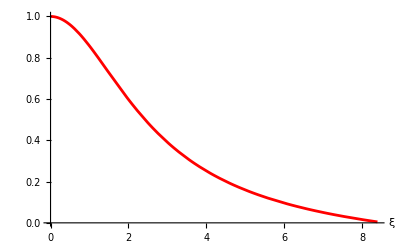

```mathematica
(*θ(ξ)*)
Plot[
lane2["Theta"][ξ],
{ξ,0,ξmax},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["ξ",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

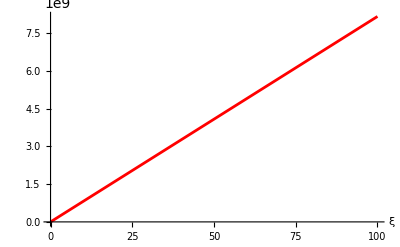

```mathematica
(*r(ξ)*)
Plot[
lane2["r"][ξ],
{ξ,0,ξmax},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["ξ",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

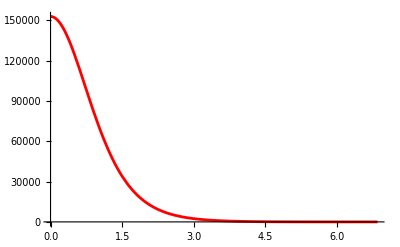

```mathematica
(*ρ(r)*)
Plot[
lane2["Rho"][r],
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

```mathematica
(*M(r)*)
Plot[
lane2["Mass"][r],
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

-Graphics-

```mathematica
(*P(r)*)
Plot[
lane2["P"][r],
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

-Graphics-

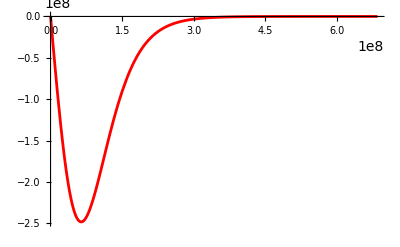

```mathematica
(*dP/dr(r)*)
Plot[
lane2["dP"][r],
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

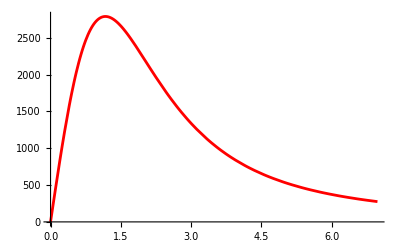

```mathematica
Plot[
lane2["g"][r],
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

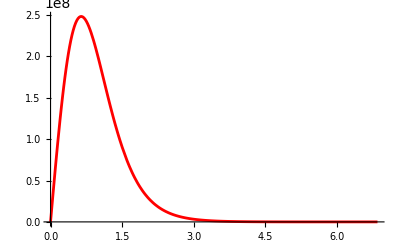

```mathematica
(*ρ(r)g(r)*)
Plot[
lane2["Rho"][r] lane2["g"][r],
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

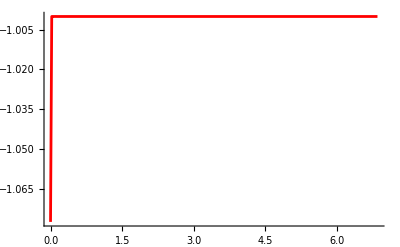

```mathematica
(*(dP/dr(r))/(ρ(r)g(r))*)
Plot[
lane2["r1"][r] ,
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

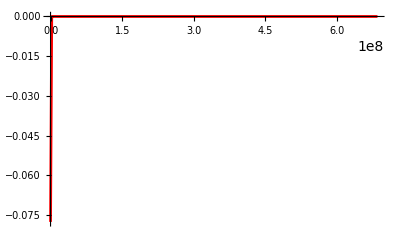

```mathematica
Plot[
lane2["B"][r] ,
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

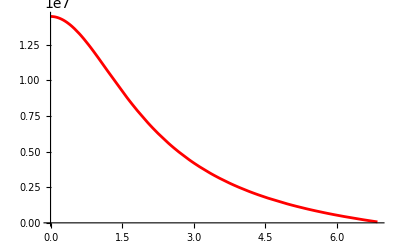

```mathematica
(*T(r)*)
Plot[
lane2["T"][r] ,
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

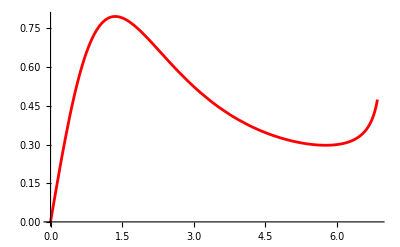

```mathematica
Plot[
lane2["F"][r] ,
{r,0,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```

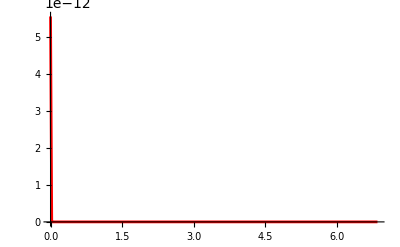

```mathematica
Plot[
lane2["L"][r] ,
{r,1,lane2["rmax"]},
PlotRange->All,
PlotStyle->Directive[Red,Thickness[0.005]],AxesLabel->{Style["",Black,18],Style["",Black,18]},
TicksStyle->Directive[Black, 14]
]
```